```mathematica
Bif figs for private assessment with bias
```

```mathematica
Global Conditions
Clear["Global`*"]
e1=0.01;
e2=0.01;
r=3;
ϵ=(1-e1)*(1-e2)+e1*e2;
e=e2;
(*ternary coords where x corresponds to freq alld, y to freq allc *)
TernCoords[x_,y_]={{1/2,-1/2},{-Tan[Pi/3]/2,-Tan[Pi/3]/2}}.{x,y}+{1/2,Tan[Pi/3]/2};
diskradius=.015;
textoffset=.05;
thickness=.005;
vlabels={Graphics[Text[Style["AllD",FontSize->Large],{-textoffset,-textoffset}]],Graphics[Text[Style["AllC",FontSize->Large],{1+textoffset,-textoffset}]],Graphics[Text[Style["Disc",FontSize->Large],{1/2,Tan[Pi/3]/2+textoffset}]]};
SetDirectory["/Users/brycemorsky/Desktop/New projects/Indirect reciprocity/figures"];
```

Conditions Global

```mathematica
Simple Standing with positive bias
g=(1-z)*gy+z*gz;
g2=(1-z)*gy^2+z*gz^2;
gb=(1-λ)*g+λ;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
piy=r*gy*z;
piz=r*gz*z-g;
zeq=Array[m,{201,2}];
geq=Array[m,{201,2}];
relgeq=Array[m,{201,2}];
realgeq=Array[m,{201,2}];
count = 1;
Do[
sol=NSolve[{
0==z*(1-z)*(piz-piy),
0==Qdg*g+1-g-gy,
0==Qcg*g2+Qdg*(g-g2)+1-g-gz,0≤z<1,0≤ gy≤ 1,0≤ gz≤ 1}/.{λ->i/200},{z,gy,gz}];
{Z,GY,GZ}=Last[SortBy[Evaluate[{z,gy,gz}/.sol],First]];
zeq[[count]]={i/200,Z};
geq[[count]]= {i/200,Z*(GY*(1-Z)+GZ*Z)};
relgeq[[count]]= {i/200,GY*(1-Z)+GZ*Z-1/(2-Z)};
realgeq[[count]]= {i/200,1/(2-Z)};
count=count+1;
,{i,0,200}]
imageSSBayes=ListLinePlot[{zeq,geq,relgeq},ImageSize->Large,PlotStyle->({#,Thickness[0.01]}&/@{ColorData[104][3],ColorData[104][16],Black}),BaseStyle->{FontSize->28},PlotRange->{{0,1},{-0.4,1}},PlotRangePadding->Scaled[.025],Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["Degree of bias, λ"],FrameStyle->None]},PlotLegends->{"z^*","z^*g^*","g^*-1/(2-z^*)"},LabelStyle->Directive[FontSize->24]];
Export["SS_private_bif_posbias.pdf",imageSSBayes];
```

bias positive Simple Standing with

```mathematica
Simple Standing with negative bias
g=x*gx+y*gy+(1-x-y)*gz;
g2=x*gx^2+y*gy^2+(1-x-y)*gz^2;
gb=(1-λ)*g;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-g;
pi=x*pix+y*piy+(1-x-y)*piz;
xeq=Array[m,{201,2}];
zeq=Array[m,{201,2}];
geq=Array[m,{201,2}];
relgeq=Array[m,{201,2}];
realgeq=Array[m,{201,2}];
count = 1;
Do[
sol1=NSolve[{
0==x*(1-x)*(pix-piz),
0==Qcg*g+1-g-gx,
0==Qcg*g2+Qdg*(g-g2)+1-g-gz,If[i<100,0,0.1]≤ x<0.9,0≤ gx≤ 1,0≤ gz≤ 1,y==0,gy==0}/.{λ->i/200},{x,y,gx,gy,gz}];
sol2=NSolve[{
0==(1-y)*y*(piz-piy),
0==Qdg*g+1-g-gy,
0==Qcg*g2+Qdg*(g-g2)+1-g-gz,0< y≤ 1,0≤ gy≤ 1,0≤ gz≤ 1,x== 0,gx==0}/.{λ->i/200},{x,y,gx,gy,gz}];
{X,Z,Y,GX,GY,GZ}=Last[SortBy[Evaluate[{x,1-x-y,y,gx,gy,gz}/.Join[sol1,sol2]],{First,Part[#,2]&}]]//.{}->Nothing;
xeq[[count]]={i/200,X};
zeq[[count]]={i/200,Z};
geq[[count]]= {i/200,X+Z*(X*GX+Y*GY+Z*GZ)};
relgeq[[count]]= {i/200,X*GX+Y*GY+Z*GZ-1/(1+Y)};
realgeq[[count]]= {i/200,1/(1+Y)};
count=count+1;
,{i,0,200}]
imageSSBayes=ListLinePlot[{xeq,zeq,geq,relgeq},ImageSize->Large,PlotStyle->({#,Thickness[0.01]}&/@{ColorData[104][6],ColorData[104][3],ColorData[104][16],Black}),BaseStyle->{FontSize->28},PlotRange->{{0,1},{-0.4,1}},PlotRangePadding->Scaled[.025],Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["Degree of bias, λ"],FrameStyle->None]},PlotLegends->{"x^*","z^*","x^*+z^*g^*","g^*-1/(1+y^*)"},LabelStyle->Directive[FontSize->24]]
Export["SS_private_bif_negbias.pdf",imageSSBayes];
```

```mathematica
g=(1-z)*Qdg+z*gz;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Qdg=(1-e)*Pdg+e*Pcg;
Solve[Qdg==gy,gy]
```

```mathematica
Staying with positive bias
g=(1-z)*gy+z*gz;
g2=(1-z)*gy^2+z*gz^2;
gb=(1-λ)*g+λ;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
piy=r*gy*z;
piz=r*gz*z-g;
zeq=Array[m,{201,2}];
geq=Array[m,{201,2}];
relgeq=Array[m,{201,2}];
realgeq=Array[m,{201,2}];
count = 1;
Do[
sol=NSolve[{
0==Qdg-gy,
0==z*(1-z)*(piz-piy),
0==(Qcg-Qdg)*g2+Qdg*g-g*gz,0≤z<1,0≤ gz≤ 1}/.{λ->i/200},{z,gy,gz}];
{Z,GY,GZ}=Last[SortBy[Evaluate[{z,gy,gz}/.sol],First]];
zeq[[count]]={i/200,Z};
geq[[count]]= {i/200,Z*(GY*(1-Z)+GZ*Z)};
relgeq[[count]]= {i/200,GY*(1-Z)+GZ*Z-Z};
count=count+1;
,{i,0,200}]
imageStBayes=ListLinePlot[{zeq,geq,relgeq},ImageSize->Large,PlotStyle->({#,Thickness[0.01]}&/@{ColorData[104][3],ColorData[104][16],Black}),BaseStyle->{FontSize->28},PlotRange->{{0,1},{-0.4,1}},PlotRangePadding->Scaled[.025],Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["Degree of bias, λ"],FrameStyle->None]},PlotLegends->{"z^*","z^*g^*","g^*-z^*)"},LabelStyle->Directive[FontSize->24]];
Export["St_private_bif_posbias.pdf",imageStBayes];
```

bias positive Staying with

bias negative Staying with

$Aborted

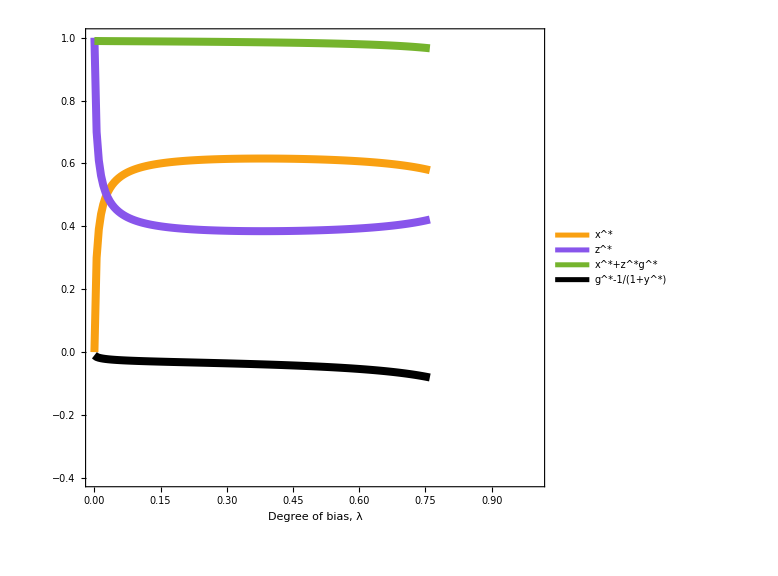

```mathematica
Staying with negative bias
g=x*gx+y*gy+(1-x-y)*gz;
g2=x*gx^2+y*gy^2+(1-x-y)*gz^2;
gb=(1-λ)*g;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-g;
pi=x*pix+y*piy+(1-x-y)*piz;
xeq=Array[m,{201,2}];
zeq=Array[m,{201,2}];
geq=Array[m,{201,2}];
relgeq=Array[m,{201,2}];
realgeq=Array[m,{201,2}];
count = 1;
Do[
sol1=NSolve[{
0==x*(1-x)*(pix-piz),
0==Qcg-gx,
0==Qcg*g2+Qdg*(g-g2)+1-g-gz,If[i<100,0,0.1]≤ x<0.9,0≤ gx≤ 1,0≤ gz≤ 1,y==0,gy==0}/.{λ->i/200},{x,y,gx,gy,gz}];
sol2=NSolve[{
0==(1-y)*y*(piz-piy),
0==Qdg-gy,
0==Qcg*g2+Qdg*(g-g2)+1-g-gz,0< y≤ 1,0≤ gy≤ 1,0≤ gz≤ 1,x== 0,gx==0}/.{λ->i/200},{x,y,gx,gy,gz}];
{X,Z,Y,GX,GY,GZ}=Last[SortBy[Evaluate[{x,1-x-y,y,gx,gy,gz}/.Join[sol1,sol2]],{First,Part[#,2]&}]]//.{}->Nothing;
xeq[[count]]={i/200,X};
zeq[[count]]={i/200,Z};
geq[[count]]= {i/200,X+Z*(X*GX+Y*GY+Z*GZ)};
relgeq[[count]]= {i/200,X*GX+Y*GY+Z*GZ-(1-Y)};
realgeq[[count]]= {i/200,1-Y};
count=count+1;
,{i,0,200}]
imageStBayes=ListLinePlot[{xeq,zeq,geq,relgeq},ImageSize->Large,PlotStyle->({#,Thickness[0.01]}&/@{ColorData[104][6],ColorData[104][3],ColorData[104][16],Black}),BaseStyle->{FontSize->28},PlotRange->{{0,1},{-0.4,1}},PlotRangePadding->Scaled[.025],Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["Degree of bias, λ"],FrameStyle->None]},PlotLegends->{"x^*","z^*","x^*+z^*g^*","g^*-x^*-z^*)"},LabelStyle->Directive[FontSize->24]]
Export["St_private_bif_negbias.pdf",imageStBayes];
```

```mathematica
old Staying with negative bias
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
gb=(1-λ)*g;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
(* Stable and unstable equilibria *)
sysStable={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qcg*g-g*gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qdg*g-g*gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*((Qcg-Qdg)*g2+Qdg*g-g*gz[t])/.{x->x[t],y->y[t]}),
gx2'[t]==(gx[t]^2-gx2[t]),
gy2'[t]==(gy[t]^2-gy2[t]),
gz2'[t]==(gz[t]^2-gz2[t])
};
eqStable1=Array[{(#-1) /1000, 0}&,1001];
eqStable2=Array[m,{1001,2}];
eqx=Array[m,{1001,2}];
coop=Array[m,{1001,2}];
count = 1;
Do[
rStable=NDSolve[Join[sysStable/.{λ->i/1000},{x[0]==0.3,y[0]==0.3,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.5,gy2[0]==0.5,gz2[0]==0.5}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,200000}];
eqStable2[[count]]= {i/1000,1-x[200000]-y[200000]/.rStable[[1]]};
eqx[[count]]= {i/1000,x[200000]/.rStable[[1]]};
coop[[count]]= {i/1000,x[200000]+(1-x[200000]-y[200000])*(gx[200000]*x[200000]+gy[200000]*y[200000]+gz[200000]*(1-x[200000]-y[200000]))/.rStable[[1]]};
count=count+1;
,{i,0,1000}];
imageStBayes=ListLinePlot[{Drop[eqStable2,-46],coop,eqx},LabelStyle->"20",ImageSize->Large,PlotStyle->({#,Thickness[0.01]}&/@{ColorData[100][8],ColorData[100][4],ColorData[100][1]}),BaseStyle->{FontSize->28},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.025],Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["Degree of bias, λ"],FrameStyle->None]}];
Export["St_private_bif_negbias.pdf",imageStBayes];
```

bias negative Staying with

```mathematica
Stern Judging with bias
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
gb=(1-λ)*g;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Pcb=(e*gb)/(e*gb+ϵ*(1-gb));
Pdb=((1-e)*gb)/((1-e)*gb+(1-ϵ)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
(* Stable and unstable equilibria *)
sysStable={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qcg*g+Qcb*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qdg*g+Qdb*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qcg*g2+(Qcb+Qdg)*(g-g2)+Qdb*(1-2*g+g2)-gz[t])/.{x->x[t],y->y[t]}),
gx2'[t]==(gx[t]^2-gx2[t]),
gy2'[t]==(gy[t]^2-gy2[t]),
gz2'[t]==(gz[t]^2-gz2[t])
};
sysUnstable={
x'[t]==-(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==-(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qcg*g+Qcb*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qdg*g+Qdb*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qcg*g2+(Qcb+Qdg)*(g-g2)+Qdb*(1-2*g+g2)-gz[t])/.{x->x[t],y->y[t]}),
gx2'[t]==(gx[t]^2-gx2[t]),
gy2'[t]==(gy[t]^2-gy2[t]),
gz2'[t]==(gz[t]^2-gz2[t])
};
eqStable1=Array[{(#-1) /1000, 0}&,1001];
eqUnstable1=Array[{(#-1) /1000, 1}&,1001];
eqStable2=Array[m,{1001,2}];
eqUnstable2=Array[m,{1001,2}];
count = 1;
Do[
rStable=NDSolve[Join[sysStable/.{λ->i/1000},{x[0]==0.3,y[0]==0.3,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.5,gy2[0]==0.5,gz2[0]==0.5}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,1000}];
rUnstable=NDSolve[Join[sysUnstable/.{λ->i/1000},{x[0]==0.2,y[0]==0.3,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.5,gy2[0]==0.5,gz2[0]==0.5}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,1000}];
eqStable2[[count]]= {i/1000,1-x[1000]-y[1000]/.rStable[[1]]};
eqUnstable2[[count]]= {i/1000,1-x[1000]-y[1000]/.rUnstable[[1]]};
count=count+1;
,{i,0,1000}];
imageSJBayes=ListLinePlot[eqStable2,LabelStyle->"20",ImageSize->Large,PlotStyle->({#,Thickness[0.01]}&/@{ColorData[100][3],ColorData[100][2],ColorData[100][3],ColorData[100][2]}),BaseStyle->{FontSize->28},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.025],Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["Degree of bias, λ"],FrameStyle->None],"Discriminators, z"}];
Export["SJ_private_bif_negbias.pdf",imageSJBayes];
```

bias Judging Stern with

```mathematica
gout[[count]]={i/1000,gx[1000]*x[1000]+gy[1000]*y[1000]+(1-x[1000]-y[1000])*gz[1000]/.rStable[[1]]};
gxout[[count]]={i/1000,gx[1000]/.rStable[[1]]};
gyout[[count]]={i/1000,gy[1000]/.rStable[[1]]};
gzout[[count]]={i/1000,gz[1000]/.rStable[[1]]};
```

NDSolve::ndsz: At t == 2.15444, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1000} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1000} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {1000} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.45917, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.38165, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

Scoring

Shunning Bayes

```mathematica
Simple Standing varying lambda
bias=1;
g=(1-z)*gy[t]+z*gz[t];
gb=(1-λ)*g+λ*bias;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Pcb=1;
Pdb=1;
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gy'[t]==Qdg*g+1-g-gy[t],
gz'[t]==Qcg*g+1-g-gz[t]
};
M=Array[m,{5151,5}];
count=1;
piy=r*gy*z;
piz=r*gz*z-(gy*(1-z)+gz*z);
pi=(1-z)*piy+z*piz;
(* Stable and unstable equilibria *)
sysStable={
z'[t]==(z*(1-z)*(piz-piy)/.{z->z[t],gy->gy[t],gz->gz[t]}),
gy'[t]==(10000*(Qdg*g+1-g-gy[t])/.{z->z[t]}),
gz'[t]==(10000*(Qcg*g+1-g-gz[t])/.{z->z[t]})
};
sysUnstable={
z'[t]==-(z*(1-z)*(piz-piy)/.{z->z[t],gy->gy[t],gz->gz[t]}),
gy'[t]==(10000*(Qdg*g+1-g-gy[t])/.{z->z[t]}),
gz'[t]==(10000*(Qcg*g+1-g-gz[t])/.{z->z[t]})
};
eqStable1=Array[m,{1001,2}];
eqUnstable1=Array[m,{1001,2}];
eqUnstable2=Array[m,{1001,2}];
eqStable2=Array[m,{1001,2}];
count = 1;
Do[
rStable=NDSolve[Join[sysStable/.{λ->i/1000},{z[0]==0.6,gy[0]==0.5,gz[0]==0.5}],{z,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
rUnstable=NDSolve[Join[sysUnstable/.{λ->i/1000},{z[0]==0.01,gy[0]==0.5,gz[0]==0.5}],{z,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
eqStable1[[count]]= {i/1000,z[10000]/.rStable[[1]]};
eqUnstable1[[count]]= {i/1000,1};
eqUnstable2[[count]]= {i/1000,z[10000]/.rUnstable[[1]]};
eqStable2[[count]]= {i/1000,0};
count=count+1;
,{i,0,1000}];
imageSSBayes=ListLinePlot[{eqUnstable1,Join[Drop[eqStable1,-138],{{863/1000,0.63
}}],Join[Drop[eqUnstable2,-137],{{863/1000,0.62
}}],eqStable2},LabelStyle->"20",ImageSize->Large,PlotStyle->({#,Thickness[0.01]}&/@{ColorData[100][2],ColorData[100][3],ColorData[100][2],ColorData[100][3]}),BaseStyle->{FontSize->28},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.025],Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["Degree of bias, λ"],FrameStyle->None],"Discriminators, z"}];
Export["lambda_SS_public_pos_bias.pdf",imageStBayes];
```

lambda Simple Standing varying

```mathematica
Staying pos bias varying lambda
bias=1;
g=(1-z)*gy[t]+z*gz[t];
gb=(1-λ)*g+λ*bias;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
repsys={
gy'[t]==Qdg-gy[t],
gz'[t]==Qcg-gz[t]
};
M=Array[m,{5151,5}];
count=1;
piy=r*gy*z;
piz=r*gz*z-(gy*(1-z)+gz*z);
pi=(1-z)*piy+z*piz;
(* Stable and unstable equilibria *)
sysStable={
z'[t]==(z*(1-z)*(piz-piy)/.{z->z[t],gy->gy[t],gz->gz[t]}),
gy'[t]==(10000*(Qdg-gy[t])/.{z->z[t]}),
gz'[t]==(10000*(Qcg-gz[t])/.{z->z[t]})
};
sysUnstable={
z'[t]==-(z*(1-z)*(piz-piy)/.{z->z[t],gy->gy[t],gz->gz[t]}),
gy'[t]==(10000*(Qdg-gy[t])/.{z->z[t]}),
gz'[t]==(10000*(Qcg-gz[t])/.{z->z[t]})
};
eqStable1=Array[m,{1001,2}];
eqUnstable1=Array[m,{1001,2}];
eqUnstable2=Array[m,{1001,2}];
eqStable2=Array[m,{1001,2}];
count = 1;
Do[
rStable=NDSolve[Join[sysStable/.{λ->i/1000},{z[0]==0.6,gy[0]==0.5,gz[0]==0.5}],{z,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
rUnstable=NDSolve[Join[sysUnstable/.{λ->i/1000},{z[0]==0.01,gy[0]==0.5,gz[0]==0.5}],{z,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
eqStable1[[count]]= {i/1000,z[10000]/.rStable[[1]]};
eqUnstable1[[count]]= {i/1000,1};
eqUnstable2[[count]]= {i/1000,z[10000]/.rUnstable[[1]]};
eqStable2[[count]]= {i/1000,0};
count=count+1;
,{i,0,1000}];
imageStBayes=ListLinePlot[{eqUnstable1,Join[Drop[eqStable1,-75],{{925/1000,0.41
}}],Join[Drop[eqUnstable2,-75],{{925/1000,0.4
}}],eqStable2},LabelStyle->"20",ImageSize->Large,PlotStyle->({#,Thickness[0.01]}&/@{ColorData[100][2],ColorData[100][3],ColorData[100][2],ColorData[100][3]}),BaseStyle->{FontSize->28},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.025],Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["Degree of bias, λ"],FrameStyle->None],"Discriminators, z"}];
Export["lambda_St_public_pos_bias.pdf",imageStBayes];
```

lambda Staying varying

```mathematica
Staying neg bias varying lambda
bias=0;
g=(1-z)*gy[t]+z*gz[t];
gb=(1-λ)*g+λ*bias;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
repsys={
gy'[t]==Qdg-gy[t],
gz'[t]==Qcg-gz[t]
};
M=Array[m,{5151,5}];
count=1;
piy=r*gy*z;
piz=r*gz*z-(gy*(1-z)+gz*z);
pi=(1-z)*piy+z*piz;
(* Stable and unstable equilibria *)
sysStable={
z'[t]==(z*(1-z)*(piz-piy)/.{z->z[t],gy->gy[t],gz->gz[t]}),
gy'[t]==(10000*(Qdg-gy[t])/.{z->z[t]}),
gz'[t]==(10000*(Qcg-gz[t])/.{z->z[t]})
};
sysUnstable={
z'[t]==-(z*(1-z)*(piz-piy)/.{z->z[t],gy->gy[t],gz->gz[t]}),
gy'[t]==(10000*(Qdg-gy[t])/.{z->z[t]}),
gz'[t]==(10000*(Qcg-gz[t])/.{z->z[t]})
};
eqStable1=Array[m,{1001,2}];
eqUnstable=Array[m,{1001,2}];
eqStable2=Array[m,{1001,2}];
count = 1;
Do[
rStable=NDSolve[Join[sysStable/.{λ->i/1000},{z[0]==0.9999,gy[0]==0.5,gz[0]==0.5}],{z,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
If[i/1000<0.2,z0=0.2,z0=0.9999];
rUnstable=NDSolve[Join[sysUnstable/.{λ->i/1000},{z[0]==z0,gy[0]==0.5,gz[0]==0.5}],{z,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
eqStable1[[count]]= {i/1000,z[10000]/.rStable[[1]]};
eqUnstable[[count]]= {i/1000,z[10000]/.rUnstable[[1]]};
eqStable2[[count]]= {i/1000,0};
count=count+1;
,{i,0,1000}];
imageStBayes=ListLinePlot[{Drop[eqStable1,-10],eqUnstable,eqStable2},LabelStyle->"20",ImageSize->Large,PlotStyle->({#,Thickness[0.01]}&/@{ColorData[100][3],ColorData[100][2],ColorData[100][3]}),BaseStyle->{FontSize->28},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.025],Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["Degree of bias, λ"],FrameStyle->None],"Discriminators, z"}];
Export["lambda_St_public_neg_bias.pdf",imageStBayes];
```

0

```mathematica
Stern Judging with negative bias
g=(1-z)*gy[t]+z*gz[t];
gb=(1-λ)*g;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Pcb=(e*gb)/(e*gb+ϵ*(1-gb));
Pdb=((1-e)*gb)/((1-e)*gb+(1-ϵ)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gy'[t]==Qdg*g+Qdb*(1-g)-gy[t],
gz'[t]==Qcg*g+Qdb*(1-g)-gz[t]
};
M=Array[m,{5151,5}];
count=1;
piy=r*gy*z;
piz=r*gz*z-(gy*(1-z)+gz*z);
pi=(1-z)*piy+z*piz;
(* Stable and unstable equilibria *)
sysStable={
z'[t]==(z*(1-z)*(piz-piy)/.{z->z[t],gy->gy[t],gz->gz[t]}),
gy'[t]==(10000*(Qdg*g+Qdb*(1-g)-gy[t])/.{z->z[t]}),
gz'[t]==(10000*(Qcg*g+Qdb*(1-g)-gz[t])/.{z->z[t]})
};
sysUnstable={
z'[t]==-(z*(1-z)*(piz-piy)/.{z->z[t],gy->gy[t],gz->gz[t]}),
gy'[t]==(10000*(Qdg*g+Qdb*(1-g)-gy[t])/.{z->z[t]}),
gz'[t]==(10000*(Qcg*g+Qdb*(1-g)-gz[t])/.{z->z[t]})
};
eqStable1=Array[m,{4001,2}];
eqUnstable1=Array[m,{4001,2}];
eqUnstable2=Array[m,{4001,2}];
eqStable2=Array[m,{4001,2}];
count = 1;
Do[
rStable=NDSolve[Join[sysStable/.{λ->i/4000},{z[0]==0.9999,gy[0]==0.5,gz[0]==0.5}],{z,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
If[i/4000<0.2,z0=0.2,z0=0.9999];
rUnstable=NDSolve[Join[sysUnstable/.{λ->i/4000},{z[0]==z0,gy[0]==0.5,gz[0]==0.5}],{z,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
eqStable1[[count]]= {i/4000,z[10000]/.rStable[[1]]};
eqUnstable1[[count]]= {i/4000,1};
eqUnstable2[[count]]= {i/4000,z[10000]/.rUnstable[[1]]};
eqStable2[[count]]= {i/4000,0};
count=count+1;
,{i,0,4000}];
imageSJBayes=ListLinePlot[{eqUnstable1,eqStable1,eqUnstable2,eqStable2},LabelStyle->"20",ImageSize->Large,PlotStyle->({#,Thickness[0.01]}&/@{ColorData[100][2],ColorData[100][3],ColorData[100][2],ColorData[100][3]}),BaseStyle->{FontSize->28},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.025],Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["Degree of bias, λ"],FrameStyle->None],"Discriminators, z"}];
Export["SJ_public_bif_negbias.pdf",imageSJBayes];
```

```mathematica
Stern Judging with bias
bias=1;
λ=0.9;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
gb=(1-λ)*g+λ*bias;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Pcb=(e*gb)/(e*gb+ϵ*(1-gb));
Pdb=((1-e)*gb)/((1-e)*gb+(1-ϵ)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gx'[t]==Qcg*g+1-g-gx[t],
gy'[t]==Qdg*g+1-g-gy[t],
gz'[t]==Qcg*g+1-g-gz[t]
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,10000},Method->"Automatic"];
M[[count]]= {0.01*i,0.01*j,gx[10000]/.R[[1]],gy[10000]/.R[[1]],gz[10000]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);
(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qcg*g+1-g-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qdg*g+1-g-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qcg*g+1-g-gz[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{81,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.00402*i,y[0]==0.00402*i,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
Eqstable[[count]]= {x[10000]/.R[[1]],y[10000]/.R[[1]]};
count=count+1;
,{i,0,80}];
dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}], (* AllC *)
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}], (* AllD *)
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}], (* Disc *)
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0.007883804914759854],diskradius]}] (* Stable equilibrium on the AllC-Disc boundary *)
};
dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageStBayes=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];
Export["SJ_public_bias.pdf",imageStBayes];
```

bias Judging Stern with

NDSolve::ndsz: At t == 0.546967, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {10000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {10000} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {10000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {10000} and/or the interpolation grid is insufficient to compute the value.

NDSolve::ndsz: At t == 0.243631, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {10000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {10000} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.210515, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

```mathematica
Stern Judging pos bias varying lambda
bias=1;
g=(1-z)*gy[t]+z*gz[t];
gb=(1-λ)*g+λ*bias;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Pcb=(e*gb)/(e*gb+ϵ*(1-gb));
Pdb=((1-e)*gb)/((1-e)*gb+(1-ϵ)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gy'[t]==Qdg*g+Qdb*(1-g)-gy[t],
gz'[t]==Qcg*g+Qdb*(1-g)-gz[t]
};
M=Array[m,{5151,5}];
count=1;
piy=r*gy*z;
piz=r*gz*z-(gy*(1-z)+gz*z);
pi=(1-z)*piy+z*piz;
(* Stable and unstable equilibria *)
sysStable={
z'[t]==(z*(1-z)*(piz-piy)/.{z->z[t],gy->gy[t],gz->gz[t]}),
gy'[t]==(10000*(Qdg*g+Qdb*(1-g)-gy[t])/.{z->z[t]}),
gz'[t]==(10000*(Qcg*g+Qdb*(1-g)-gz[t])/.{z->z[t]})
};
sysUnstable={
z'[t]==-(z*(1-z)*(piz-piy)/.{z->z[t],gy->gy[t],gz->gz[t]}),
gy'[t]==(10000*(Qdg*g+Qdb*(1-g)-gy[t])/.{z->z[t]}),
gz'[t]==(10000*(Qcg*g+Qdb*(1-g)-gz[t])/.{z->z[t]})
};
eqStable1=Array[m,{1001,2}];
eqUnstable1=Array[m,{1001,2}];
eqUnstable2=Array[m,{1001,2}];
eqStable2=Array[m,{1001,2}];
count = 1;
Do[
rStable=NDSolve[Join[sysStable/.{λ->i/1000},{z[0]==0.6,gy[0]==0.5,gz[0]==0.5}],{z,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
rUnstable=NDSolve[Join[sysUnstable/.{λ->i/1000},{z[0]==0.01,gy[0]==0.5,gz[0]==0.5}],{z,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
eqStable1[[count]]= {i/1000,z[10000]/.rStable[[1]]};
eqUnstable1[[count]]= {i/1000,1};
eqUnstable2[[count]]= {i/1000,z[10000]/.rUnstable[[1]]};
eqStable2[[count]]= {i/1000,0};
count=count+1;
,{i,0,1000}];
imageSJBayes=ListLinePlot[{eqUnstable1,Join[Drop[eqStable1,-137],{{864/1000,0.62
}}],Join[Drop[eqUnstable2,-136],{{864/1000,0.62
}}],eqStable2},LabelStyle->"20",ImageSize->Large,PlotStyle->({#,Thickness[0.01]}&/@{ColorData[100][2],ColorData[100][3],ColorData[100][2],ColorData[100][3]}),BaseStyle->{FontSize->28},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.025],Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["Degree of bias, λ"],FrameStyle->None],"Discriminators, z"}];
Export["lambda_SJ_public_pos_bias.pdf",imageSJBayes];
```

0

```mathematica
Stern Judging neg bias varying lambda
bias=0;
g=x*gx[t]+(1-z)*gy[t]+z*gz[t];
gb=(1-λ)*g+λ*bias;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Pcb=(e*gb)/(e*gb+ϵ*(1-gb));
Pdb=((1-e)*gb)/((1-e)*gb+(1-ϵ)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gx'[t]==Qcg*g+Qcb*(1-g)-gx[t],
gy'[t]==Qdg*g+Qdb*(1-g)-gy[t],
gz'[t]==Qcg*g+Qdb*(1-g)-gz[t]
};
M=Array[m,{5151,5}];
count=1;
pix=r*(x+gx*z)-1;
piy=r*(x+gy*z);
piz=r*(x+gz*z)-(gx*x+gy*(1-x-z)+gz*z);
pi=x*pix+(1-x-z)*piy+z*piz;
(* Stable and unstable equilibria *)
sysStable={
x'[t]==(x*(pix-pi)/.{x->x[t],z->z[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
z'[t]==(z*(piz-pi)/.{x->x[t],z->z[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qcg*g+Qcb*(1-g)-gx[t])/.{x->x[t],z->z[t]}),
gy'[t]==(10000*(Qdg*g+Qdb*(1-g)-gy[t])/.{x->x[t],z->z[t]}),
gz'[t]==(10000*(Qcg*g+Qdb*(1-g)-gz[t])/.{x->x[t],z->z[t]})
};
sysUnstable={
x'[t]==-(x*(pix-pi)/.{x->x[t],z->z[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
z'[t]==-(z*(piz-pi)/.{x->x[t],z->z[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qcg*g+Qcb*(1-g)-gx[t])/.{x->x[t],z->z[t]}),
gy'[t]==(10000*(Qdg*g+Qdb*(1-g)-gy[t])/.{x->x[t],z->z[t]}),
gz'[t]==(10000*(Qcg*g+Qdb*(1-g)-gz[t])/.{x->x[t],z->z[t]})
};
eqStable1=Array[m,{1001,2}];
eqUnstable=Array[m,{1001,2}];
eqStable2=Array[m,{1001,2}];
count = 1;
Do[
rStable=NDSolve[Join[sysStable/.{λ->i/1000},{x[0]==0.1,z[0]==0.8,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,z,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
rUnstable=NDSolve[Join[sysUnstable/.{λ->i/1000},{x[0]==0.8,z[0]==0.1,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,z,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
eqStable1[[count]]= {i/1000,z[10000]/.rStable[[1]]};
eqUnstable[[count]]= {i/1000,z[10000]/.rUnstable[[1]]};
eqStable2[[count]]= {i/1000,0};
count=count+1;
,{i,0,1000}];
imageSJBayes=ListLinePlot[{eqStable1,eqUnstable,eqStable2},LabelStyle->"20",ImageSize->Large,PlotStyle->({#,Thickness[0.01]}&/@{ColorData[100][3],ColorData[100][2],ColorData[100][3]}),BaseStyle->{FontSize->28},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.025],Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{Framed[Style["Degree of bias, λ"],FrameStyle->None],"Discriminators, z"}];
Export["lambda_SJ_public_neg_bias.pdf",imageSJBayes];
```

bias Judging lambda neg Stern varying

```mathematica
Stern Judging neg bias varying lambda
bias=0;
g=x*gx[t]+(1-z)*gy[t]+z*gz[t];
gb=(1-λ)*g+λ*bias;
Pcg=(ϵ*gb)/(ϵ*gb+e*(1-gb));
Pdg=((1-ϵ)*gb)/((1-ϵ)*gb+(1-e)*(1-gb));
Pcb=(e*gb)/(e*gb+ϵ*(1-gb));
Pdb=((1-e)*gb)/((1-e)*gb+(1-ϵ)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gx'[t]==Qcg*g+Qcb*(1-g)-gx[t],
gy'[t]==Qdg*g+Qdb*(1-g)-gy[t],
gz'[t]==Qcg*g+Qdb*(1-g)-gz[t]
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,100000},Method->"Automatic"];
M[[count]]= {0.01*i,0.01*j,gx[100000]/.R[[1]],gy[100000]/.R[[1]],gz[100000]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);
(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qcg*g+Qcb*(1-g)-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qdg*g+Qdb*(1-g)-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qcg*g+Qdb*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{81,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.00402*i,y[0]==0.00402*i,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,10000},Method->"StiffnessSwitching"];
Eqstable[[count]]= {x[10000]/.R[[1]],y[10000]/.R[[1]]};
count=count+1;
,{i,0,80}];
dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}], (* AllC *)
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}], (* AllD *)
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}], (* Disc *)
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0.6344012585668878,0],diskradius]}] (* Stable equilibrium on the AllC-Disc boundary *)
};
dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSJBayes=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];
Export["SJ_public_bias_test.pdf",imageSJBayes];
```

0

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {gx'[t]==-gx[t]+(1.-(1+Times[«2»]) gy[t]-z gz[t]) ((0.019602 («1») (0.+Times[«2»]+Times[«2»]))/Plus[«2»]+(0.009802 (1+«1») («1»))/Plus[«2»])+(0.+(1+Times[«2»]) gy[t]+z gz[t]) ((0.960792 (1+Times[«2»]) (0.+Times[«2»]+Times[«2»]))/Plus[«2»]+(0.00039204 (1+Times[«2»]) (0.+Times[«2»]+Times[«2»]))/Plus[«2»]),gy'[t]==«1»,«3»,gz[0]==0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {x'[t]==x[t] (-1-x[t] (-1+3 Plus[«2»])+3 (x[t]+gx[«1»] Plus[«3»])-3 (x[t]+gy[«1»] Plus[«3»]) y[t]-(1-x[«1»]-y[«1»]) (-gx[«1»] x[«1»]+3 Plus[«2»]-gz[«1»] Plus[«3»]-gy[«1»] y[«1»])),«8»,gz[0]==0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: {x'[t]==x[t] (-1-x[t] (-1+3 Plus[«2»])+3 (x[t]+gx[«1»] Plus[«3»])-3 (x[t]+gy[«1»] Plus[«3»]) y[t]-(1-x[«1»]-y[«1»]) (-gx[«1»] x[«1»]+3 Plus[«2»]-gz[«1»] Plus[«3»]-gy[«1»] y[«1»])),«8»,gz[0]==0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve::ndnum will be suppressed during this calculation.

ReplaceAll::reps: {gx'[t]==-1. gx[t]+(1.-1. (1.+Times[«2»]) gy[t]-1. z gz[t]) ((0.019602 («1») («1»))/Plus[«2»]+(«1»)/Plus[«2»])+(0.+(1.+Times[«2»]) gy[t]+z gz[t]) ((0.960792 (1.+Times[«2»]) (0.+Times[«2»]+Times[«2»]))/Plus[«2»]+(0.00039204 (1.+Times[«2»]) (0.+Times[«2»]+Times[«2»]))/Plus[«2»]),«4»,gz[0]==0.5} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Staying with negative bias
bias=0;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
gb=(1-λ)*g+λ*bias;
Pcg=ϵ*gb/(ϵ*gb+e*(1-gb));
Pdg=(1-ϵ)*gb/((1-ϵ)*gb+(1-e)*(1-gb));
Pcb=e*gb/(e*gb+ϵ*(1-gb));
Pdb=(1-e)*gb/((1-e)*gb+(1-ϵ)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gx'[t]==Qcg*g-g*gx[t],
gy'[t]==Qdg*g-g*gy[t],
gz'[t]==(Qcg-Qdg)*g2+Qdg*g-g*gz[t],
gx2'[t]==(gx[t]^2-gx2[t]),
gy2'[t]==(gy[t]^2-gy2[t]),
gz2'[t]==(gz[t]^2-gz2[t])
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,100000},Method->"Automatic"];
M[[count]]= {0.01*i,0.01*j,gx[100000]/.R[[1]],gy[100000]/.R[[1]],gz[100000]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);
(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qcg*g-g*gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qdg*g-g*gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*((Qcg-Qdg)*g2+Qdg*g-g*gz[t])/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*(gx[t]^2-gx2[t])/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*(gy[t]^2-gy2[t])/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*(gz[t]^2-gz2[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{81,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.00402*i,y[0]==0.00402*i,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,1000000},Method->"StiffnessSwitching"];
Eqstable[[count]]= {x[1000000]/.R[[1]],y[1000000]/.R[[1]]};
count=count+1;
,{i,0,80}];
dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}], (* AllC *)
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}], (* AllD *)
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}], (* Disc *)
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0.6344012585668878,0],diskradius]}] (* Stable equilibrium on the AllC-Disc boundary *)
};
dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageStBayes=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];
Export["St_public_neg_bias.pdf",imageStBayes];
```

0

```mathematica
Staying with positive bias
bias=1;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
gb=(1-λ)*g+λ*bias;
Pcg=ϵ*gb/(ϵ*gb+e*(1-gb));
Pdg=(1-ϵ)*gb/((1-ϵ)*gb+(1-e)*(1-gb));
Pcb=e*gb/(e*gb+ϵ*(1-gb));
Pdb=(1-e)*gb/((1-e)*gb+(1-ϵ)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gx'[t]==Qcg*g-g*gx[t],
gy'[t]==Qdg*g-g*gy[t],
gz'[t]==(Qcg-Qdg)*g2+Qdg*g-g*gz[t],
gx2'[t]==(gx[t]^2-gx2[t]),
gy2'[t]==(gy[t]^2-gy2[t]),
gz2'[t]==(gz[t]^2-gz2[t])
};
M=Array[m,{5151,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.01*i,y->0.01*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,100000},Method->"Automatic"];
M[[count]]= {0.01*i,0.01*j,gx[100000]/.R[[1]],gy[100000]/.R[[1]],gz[100000]/.R[[1]]};
count=count+1;
,{i,0,100},{j,0,100-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);
(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qcg*g-g*gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qdg*g-g*gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*((Qcg-Qdg)*g2+Qdg*g-g*gz[t])/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*(gx[t]^2-gx2[t])/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*(gy[t]^2-gy2[t])/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*(gz[t]^2-gz2[t])/.{x->x[t],y->y[t]})
};
Eqstable=Array[m,{81,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys,{x[0]==0.00402*i,y[0]==0.00402*i,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,1000000},Method->"StiffnessSwitching"];
Eqstable[[count]]= {x[1000000]/.R[[1]],y[1000000]/.R[[1]]};
count=count+1;
,{i,0,80}];
dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}], (* AllC *)
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}], (* AllD *)
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}], (* Disc *)
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0.007883804914759854],diskradius]}] (* Stable equilibrium on the AllC-Disc boundary *)
};
dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageStBayes=Show[ternplot,dots,vlabels, ImageSize->Large,PlotRangePadding->.1];
Export["St_public_pos_bias.pdf",imageStBayes];
```

```mathematica
Simple Standing varying lambda;
bias=1;
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
gb=(1-λ)*g+λ*bias;
Pcg=ϵ*gb/(ϵ*gb+e*(1-gb));
Pdg=(1-ϵ)*gb/((1-ϵ)*gb+(1-e)*(1-gb));
Pcb=e*gb/(e*gb+ϵ*(1-gb));
Pdb=(1-e)*gb/((1-e)*gb+(1-ϵ)*(1-gb));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gx'[t]==Qcg*g-g*gx[t],
gy'[t]==Qdg*g-g*gy[t],
gz'[t]==(Qcg-Qdg)*g2+Qdg*g-g*gz[t],
gx2'[t]==(gx[t]^2-gx2[t]),
gy2'[t]==(gy[t]^2-gy2[t]),
gz2'[t]==(gz[t]^2-gz2[t])
};
M=Array[m,{5151,5}];
count=1;
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
(* Stable equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(10000*(Qcg*g-g*gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(10000*(Qdg*g-g*gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(10000*(Qcg*g-g*gz[t])/.{x->x[t],y->y[t]}),
gx2'[t]==(10000*(gx[t]^2-gx2[t])/.{x->x[t],y->y[t]}),
gy2'[t]==(10000*(gy[t]^2-gy2[t])/.{x->x[t],y->y[t]}),
gz2'[t]==(10000*(gz[t]^2-gz2[t])/.{x->x[t],y->y[t]})
};
lambdax=Array[m,{1001,2}];
lambday=Array[m,{1001,2}];
coop=Array[m,{1001,2}];
count = 1;
Do[
R=NDSolve[Join[fullsys/.{λ->i/1000},{x[0]==0.05,y[0]==0.5,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{x,y,gx,gy,gz,gx2,gy2,gz2},{t,0,1000000},Method->"StiffnessSwitching"];
lambdax[[count]]= {i/1000,x[1000000]/.R[[1]]};
lambday[[count]]= {i/1000,y[1000000]/.R[[1]]};
coop[[count]]={i/1000,(x[1000000]+(1-x[1000000]-y[1000000])*(x[1000000]*gx[1000000]+y[1000000]*gy[1000000]+(1-x[1000000]-y[1000000])*gz[1000000]))/.R[[1]]};
count=count+1;
,{i,0,1000}];
```

NDSolve::ndsz: At t == 0.247463, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {1000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1000000} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {1000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1000000} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {1000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {1000000} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

NDSolve::ndsz: At t == 0.440027, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.518814, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

```mathematica
imageStBayes=ListLinePlot[{Callout[lambday,"frequency of AllD, y",{0.5,Above}],Callout[coop,"intentions of cooperation, x+gz",{0.55,Below}]},LabelStyle->"20",ImageSize->Large,PlotStyle->({#,Thickness[0.01]}&/@{ColorData[100][2],ColorData[100][3]}),BaseStyle->{FontSize->28},PlotRange->{{0,1},{0,1}},PlotRangePadding->Scaled[.025],Frame->{{True,False},{True,False}},FrameStyle->{{Black,None},{Black,None}},AspectRatio->1,FrameLabel->{"Degree of bias, λ",None}];
Export["lambda_St_public_neg_bias.pdf",imageStBayes];
```

InterpolatingFunction::dmval: Input value {1.×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1.×10^6} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {1.×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {1.×10^6} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {1.×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {1.×10^6} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.